# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Resonant_k\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Grid

```mathematica
radius=2;
delta=0.02;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

## Method

```mathematica
(*Floquet parameters*)
J=10;
k=Pi(2/5.);
```

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
F=MatrixExp[-I*k*ops[[3]]];
```

```mathematica
{neweigenval,neweigenvec}=Eigensystem[F];
```

```mathematica
neweigenvec=Orthogonalize[neweigenvec];
```

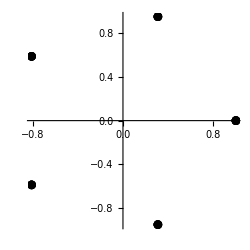

```mathematica
ComplexListPlot[neweigenval,PlotRange->All,AspectRatio->1,ImageSize->250,PlotStyle->Directive[Black,PointSize[0.025]]]
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->500,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
(*Export["d2_J_"<>ToString[J]<>"alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>"_.png",plot]*)
```

-Graphics-

## Husimis

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,1,2J+1}];
```

## Symmetric states

```mathematica
(* Floquet parameters *)
J = 10;
k = Pi (1/5.);
(* Note: Assuming α is defined earlier in your notebook *)
ops = generateSpinOperators[J];
```

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
```

```mathematica
(* Diagonalize Jx to get pure m-states *)
{mValues, jxBasis} = Eigensystem[ops[[3]]];
mValues = Round[Re[mValues]];

(* Group and sum to create the 5 true states *)
pairedStates = Transpose[{mValues, jxBasis}];
sectors = GatherBy[pairedStates, Mod[#[[1]], 5] &];
trueStates = Map[Normalize[Total[#[[All, 2]]]] &, sectors];

(* Define a function to compute and plot a single sector *)
plotSector[state_, sectorIndex_] := Module[
  {newdata, husi, husiLog, plotHusimi, plotZeros},
  
  (* Calculate the Husimi Q-function *)
  newdata = ParallelMap[
    Abs[state . Conjugate[#]]^2 &, 
    statesCompiled, 
    Method -> "CoarsestGrained"
  ];
  
  (* Format data arrays *)
  husi = Transpose[{region[[All, 1]], region[[All, 2]], newdata}];
  
  (* Add 10^-16 to prevent Log[0] crashes at the exact nodes *)
  husiLog = Transpose[{region[[All, 1]], region[[All, 2]], Log[newdata + 10^-16]}];
  
  (* Generate Left Plot: Standard Husimi *)
  plotHusimi = ListDensityPlot[husi, PlotRange -> All, PlotTheme -> "Detailed", 
    ColorFunction -> "BlueGreenYellow", 
    PlotLabel -> Style["Husimi: Sector " <> ToString[sectorIndex], 20, Black], 
    ImageSize -> 400, 
    FrameLabel -> {Style["Q", 20, Black], Rotate[Style["P", 20, Black], -90 Degree]}, 
    LabelStyle -> Directive[15, Black], AspectRatio -> 1, Frame -> True, 
    InterpolationOrder -> 1];
    
  (* Generate Right Plot: Zeros (Log Scale) *)
  plotZeros = ListDensityPlot[husiLog, PlotRange -> All, PlotTheme -> "Detailed", 
    ColorFunction -> "BlueGreenYellow", 
    PlotLabel -> Style["Zeros (Log): Sector " <> ToString[sectorIndex], 20, Black], 
    ImageSize -> 400, 
    FrameLabel -> {Style["Q", 20, Black], Rotate[Style["P", 20, Black], -90 Degree]}, 
    LabelStyle -> Directive[15, Black], AspectRatio -> 1, Frame -> True, 
    InterpolationOrder -> 1];
    
  (* Combine them side-by-side *)
  GraphicsRow[{plotHusimi, plotZeros}, ImageSize -> 850]
]

(* Loop over all 5 true states, generate their paired plots, and stack them *)
allPlots = Table[plotSector[trueStates[[i]], i], {i, 1, Length[trueStates]}];
Column[allPlots, Spacings -> 2]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

# Levels

```mathematica
(* ── Parameters ── *)
J = 40;
k =(2*Pi)(1/6);
alist = Range[0,Pi, Pi/1000]/Pi;
alist//Length
```

1001

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
resultsphi = ParallelTable[
  Module[{F, eigenvalM, eigenvalm,A=ops[[4]],B=ops[[3]]},
F=MatrixExp[-I*k*A].MatrixExp[-I*a*Pi*B];
eigenvalM=Eigenvalues[F];
Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}]
 ],{a, alist},Method -> "CoarsestGrained"];
```

```mathematica
levelsM = Transpose[resultsphi];
test=ListPlot[
  Flatten[levelsM, 1],
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α/π", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k/2π = ", NumberForm[k/(2Pi), {4,2}]}], 25, Black],
  AspectRatio -> 0.4, ImageSize -> 900,
  PlotRange -> All
];
Export["levels_J_"<>ToString[J]<>"_k_"<>ToString[N[k/(2*Pi)]]<>"_.png",test]
```

levels_J_40_k_0.166667_.png

```mathematica
(* ── Parameters ── *)
J = 40;
alist = Range[0,Pi, Pi/1000]/Pi;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
(* 1. Define the function to compute the number of unperturbed bands *)
(* This calculates the cardinality of the set of unique quadratic residues modulo q *)
NumberOfBands[q_Integer] := Length[Union[Mod[Range[0, q - 1]^2, q]]]

(* 2. Define the search algorithm to find the simplest fraction 1/q *)
(* We set a maximum search limit to prevent infinite loops on mathematically impossible band counts (like n = 5) *)
GenerateFraction[n_Integer] := Module[{q = 1, maxSearch = 4000},
  While[NumberOfBands[q] != n && q <= maxSearch, 
   q++
  ];
  
  If[q <= maxSearch, 
   1/q, 
   "Impossible"
  ]
]
```

```mathematica
(* 3. Execute the algorithm for the first 12 target band counts *)
targetBands = Range[1, 10];
results = Table[{n, GenerateFraction[n]}, {n, targetBands}];

(* 4. Output the results in a strictly formatted grid *)
Grid[
 Prepend[results, {"Target Bands (n)", "Generating Fraction (k/2π)"}],
 Frame -> All,
 Background -> {None, {LightGray, None}},
 Alignment -> Center
]
```

Target Bands (n) | Generating Fraction (k/2π)
1 | 1
2 | 1/2
3 | 1/5
4 | 1/6
5 | Impossible
6 | 1/10
7 | 1/13
8 | 1/14
9 | 1/17
10 | 1/19

```mathematica
list=DeleteCases[results[[All,2]],"Impossible"]
```

{1,1/2,1/5,1/6,1/10,1/13,1/14,1/17,1/19}

```mathematica
list=Table[1/i,{i,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Table[
k =(2*Pi)(b);
resultsphi = ParallelTable[
  Module[{F, eigenvalM, eigenvalm,A=ops[[4]],B=ops[[3]]},
F=MatrixExp[-I*k*A].MatrixExp[-I*a*Pi*B];
eigenvalM=Eigenvalues[F];
Transpose[{ConstantArray[a, Length[eigenvalM]], Arg[eigenvalM]}]
 ],{a, alist},Method -> "CoarsestGrained"];
levelsM = Transpose[resultsphi];
test=ListPlot[
  Flatten[levelsM, 1],
  PlotStyle -> {Directive[Black, PointSize[0.0015]], Directive[Red, PointSize[0.0015]]},
  Axes -> False, Frame -> True,
  FrameLabel -> {Style["α/π", 30, Black], Style["φ", 30, Black]},
  GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
  FrameStyle -> Directive[Black, 24, Thickness[0.0015]],
  LabelStyle -> Directive[Black, 24],
  PlotLabel -> Style[Row[{"Levels, J = ", J, ", k/2π = ", NumberForm[k/(2Pi), {4,2}]}], 25, Black],
  AspectRatio -> 0.4, ImageSize -> 900,
  PlotRange -> All
];
Export["levels_J_"<>ToString[J]<>"_k_"<>ToString[N[k/(2*Pi)]]<>"_.png",test]
,{b,list}]
```

{levels_J_40_k_1._.png,levels_J_40_k_0.5_.png,levels_J_40_k_0.333333_.png,levels_J_40_k_0.25_.png,levels_J_40_k_0.2_.png,levels_J_40_k_0.166667_.png,levels_J_40_k_0.142857_.png,levels_J_40_k_0.125_.png,levels_J_40_k_0.111111_.png,levels_J_40_k_0.1_.png}